```mathematica
<<RQA`
```

```mathematica
α=1.4;β=0.3;nMax=2000;settle=40;
```

```mathematica
henonxy=
Drop[RecurrenceTable[{x[n+1]==1-α x[n]^2+y[n],
y[n+1]==β x[n],x[0]==0.0,y[0]==0.0},{x,y},{n,1,nMax+settle},DependentVariables->{x,y}],settle];
```

```mathematica
hts=TimeSeries[TemporalData[henonxy,{1,Automatic,1},ValueDimensions->2]]
```

TimeSeries[…]

```mathematica
tStart=1001;
w=200;
```

```mathematica
hw=TimeSeriesWindow[hts,{tStart,tStart+w-1}]
```

TimeSeries[…]

```mathematica
hx=TimeSeries[TemporalData[hw["Values"][[All,1]],{tStart,tStart+w-1,1}]]
```

TimeSeries[…]

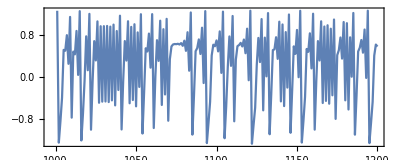

```mathematica
ListLinePlot[hx,Axes->None,Frame->True,AspectRatio->.4]
```

```mathematica
hxe3=RQAEmbed[hx,3,1.0]
```

TimeSeries[…]

```mathematica
dm=RQADistanceMap[hxe3,DistanceFunction->EuclideanDistance];
```

```mathematica
ArrayPlot[dm,DataReversed->True,PlotLegends->Automatic,FrameTicks->None,ColorFunction->ColorData["Temperature"],ImageSize->500,FrameLabel->{"time","time",None,None}]
```

-Graphics-

```mathematica
rm=RQARecurrenceMap[hxe3,0.03,"Rescale"->True,DistanceFunction->EuclideanDistance]
```

SparseArray[…]

```mathematica
ArrayPlot[rm,DataReversed->True,FrameTicks->None,ImageSize->500,PlotLegends->Automatic]
```

-Graphics-

```mathematica
rm2=RQARecurrenceMap[dm,0.03]
```

SparseArray[…]

```mathematica
ArrayPlot[rm2,DataReversed->True,FrameTicks->None,ImageSize->500,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Manipulate[ArrayPlot[
RQARecurrenceMap[dm,τ],
DataReversed->True,FrameTicks->None,ImageSize->500,PlotLegends->Automatic,PlotRange->{0,τ}],
{{τ,.01},0.,.2}]
```

The heaviside function doesn’t evaulate where it is very close to 0. Unitize does... all these distances are positive, so we’re good.

```mathematica
RQAVerticalLineLengths[Unitize[Normal[rm2]]]
```

{2,3,4,4,5}

```mathematica
Unitize[rm2]
```

SparseArray[…]

```mathematica
Dimensions[rm2]
```

{198,198}

```mathematica
rm["Properties"]
```

{AdjacencyLists,Background,ColumnIndices,Density,MatrixColumns,NonzeroValues,PatternArray,Properties,RowPointers}

```mathematica
rm["NonzeroValues"]
```

{0.0106693,0.0249243,0.00196787,0.0107825,0.0275007,0.00507174,0.0282317,0.00762521,0.0239732,0.0236637,0.0102094,0.0249858,0.014839,0.0154976,0.0145904,0.0263253,0.0159462,0.0242202,0.0265615,0.0284154,0.0267448,0.0222395,0.0158191,0.0229825,0.0283915,0.0131038,0.0157461,0.0208371,0.0188162,0.0194943,0.0251276,0.02332,0.0270436,0.0218824,0.0190599,0.0115214,0.0115146,0.00163855,0.0016413,0.00142013,0.00121322,0.0293468,0.00141814,0.00141923,0.00775469,0.0264865,0.0261337,0.000686719,0.025665,0.00337862,0.0144598,0.0130336,0.0015158,0.0193897,0.0286211,0.00523485,0.0232173,0.0138355,0.00235495,0.0292064,0.0245199,0.00697613,0.0084125,0.00935201,0.0291744,0.0113892,0.00512501,0.018103,0.00169835,0.00418775,0.0126057,0.0161481,0.00734969,0.0211745,0.00697613,0.00381287,0.00793093,0.0270211,0.0143514,0.00934886,0.0153849,0.00169835,0.00559619,0.0111027,0.0146957,0.0291548,0.00592704,0.0226518,0.0084125,0.00381287,0.0117362,0.0232139,0.0177447,0.0299698,0.0266272,0.0121888,0.0115799,0.0286211,0.00418775,0.00559619,0.0166979,0.0202805,0.0297667,0.0292004,0.0114907,0.0170566,0.00935201,0.00793093,0.0117362,0.00801792,0.00670689,0.0233146,0.0126057,0.0111027,0.0166979,0.00366197,0.00528729,0.0298201,0.0291744,0.0270211,0.0232139,0.00675953,0.00784273,0.0116369,0.0269492,0.0106482,0.0268784,0.00803887,0.0180814,0.0216255,0.0168642,0.0227643,0.0179236,0.0264576,0.0115146,0.0123823,0.0016413,0.0298941,0.00128121,0.00121322,0.0285751,0.00090323,0.00141923,0.00652127,0.0252204,0.0260582,0.000761236,0.0257579,0.00337862,0.0110922,0.0159564,0.0018639,0.0225748,0.00523485,0.0179832,0.0190655,0.00287994,0.0276293,0.0297525,0.0113892,0.0143514,0.0177447,0.00801792,0.00626416,0.0289024,0.0161481,0.0146957,0.0202805,0.00366197,0.00879918,0.0299698,0.00675953,0.00890506,0.0183905,0.0206753,0.0106482,0.0028033,0.0287277,0.0216255,0.00476584,0.0227643,0.00484994,0.00639584,0.0217443,0.0141034,0.0142205,0.0220194,0.0261068,0.0166718,0.0183398,0.0286793,0.0210008,0.0230007,0.0291091,0.014839,0.028707,0.0293071,0.00502999,0.0263253,0.0210121,0.00514278,0.02332,0.0230406,0.0239376,0.0053434,0.0190599,0.0112645,0.0292058,0.0298941,0.0296008,0.0293468,0.0285751,0.0279531,0.00775469,0.00652127,0.0187333,0.0230443,0.00709326,0.0234962,0.0144598,0.0110922,0.0260238,0.0129456,0.0232173,0.0268784,0.0179832,0.0208628,0.0294886,0.00976433,0.00728084,0.0131873,0.0183164,0.0278055,0.0049835,0.027831,0.00524122,0.0282254,0.0127167,0.0152181,0.015034,0.0174912,0.018409,0.027104,0.00840272,0.0199598,0.0127167,0.00369119,0.00312242,0.00835862,0.0117672,0.0258741,0.0270047,0.0148787,0.0163876,0.0152181,0.00369119,0.00522453,0.00492712,0.0146398,0.0226623,0.0247924,0.0154839,0.0196034,0.015034,0.00312242,0.00522453,0.0101294,0.00942015,0.0278744,0.0297436,0.017942,0.0144753,0.0174912,0.00835862,0.00492712,0.0101294,0.0195491,0.0177455,0.0205736,0.0152206,0.0245283,0.0258035,0.018409,0.0117672,0.0146398,0.00942015,0.0195491,0.0243527,0.00543345,0.0258741,0.0226623,0.0278744,0.0177455,0.0103891,0.0237889,0.0080643,0.0252517,0.00451884,0.01679,0.0171162,0.00633826,0.0272913,0.0206127,0.0210121,0.0148874,0.01712,0.0283915,0.0270436,0.0230406,0.0154087,0.0177169,0.0266699,0.0217443,0.00764144,0.00363995,0.0261068,0.00943918,0.00260186,0.0239732,0.0118608,0.0291768,0.00328508,0.0168295,0.0046195,0.0252517,0.0207345,0.0112667,0.00907375,0.0285934,0.00771767,0.0143373,0.0189784,0.0185798,0.0180246,0.0106693,0.0146976,0.012611,0.00278904,0.0275007,0.000765523,0.00119585,0.00148524,0.027831,0.0285809,0.00229354,0.027104,0.0270047,0.0247924,0.0297436,0.0205736,0.0103891,0.0189276,0.0128487,0.00451884,0.0207345,0.0127216,0.0126847,0.00633826,0.0285934,0.0209601,0.0142775,0.0222395,0.0148874,0.0131038,0.0154087,0.0287281,0.0188162,0.0266699,0.0168655,0.027827,0.0159462,0.0239376,0.0285872,0.0265615,0.0183164,0.0049835,0.00524122,0.0285809,0.0285542,0.00840272,0.0148787,0.0154839,0.017942,0.0152206,0.0243527,0.0237889,0.0189276,0.0270801,0.0199598,0.0163876,0.0196034,0.0144753,0.0245283,0.00543345,0.0270801,0.0258035,0.0080643,0.0128487,0.01679,0.0112667,0.0127216,0.00932401,0.0272913,0.00771767,0.0209601,0.00683521,0.0189784,0.0206684,0.0156328,0.0185798,0.0202973,0.0152689,0.0180246,0.0201165,0.0148521,0.0249243,0.0146976,0.0268905,0.0141574,0.0168655,0.027827,0.0242202,0.0264865,0.0252204,0.0187333,0.0260073,0.0258211,0.028417,0.0260717,0.00601777,0.00289828,0.00349313,0.0141034,0.00764144,0.0277466,0.00847043,0.0166718,0.00943918,0.0120181,0.0236637,0.0210008,0.0118608,0.0243976,0.0151447,0.0154976,0.028707,0.0168295,0.0297134,0.0214487,0.00579923,0.0261337,0.0260582,0.0230443,0.0260073,0.0259453,0.00310038,0.0130336,0.0159564,0.0260238,0.0142983,0.00724519,0.0138355,0.0291548,0.0297667,0.0190655,0.0161876,0.0107011,0.0266272,0.00784273,0.00890506,0.0159401,0.0234489,0.00803887,0.0028033,0.026079,0.0168642,0.00476584,0.0179236,0.00484994,0.0264576,0.00639584,0.0142205,0.0277466,0.0183398,0.0230007,0.0293071,0.0291431,0.0158191,0.0206684,0.00888631,0.0157461,0.0287281,0.0202973,0.00512678,0.0194943,0.0201165,0.00564249,0.00196787,0.012611,0.0268905,0.0127447,0.00507174,0.00762521,0.0102094,0.0291091,0.0291768,0.0243976,0.0145904,0.0267448,0.00502999,0.0297134,0.0291431,0.00514278,0.01712,0.0218824,0.0053434,0.0177169,0.0285872,0.0115214,0.0112645,0.00163855,0.0123823,0.0292058,0.00142013,0.00128121,0.0296008,0.00141814,0.00090323,0.0279531,0.000686719,0.000761236,0.00709326,0.0258211,0.0259453,0.0255563,0.0015158,0.0018639,0.0129456,0.0142983,0.0207964,0.00235495,0.0292004,0.00287994,0.0208628,0.0161876,0.0283956,0.0268737,0.00512501,0.00934886,0.0121888,0.00670689,0.00626416,0.0228933,0.00734969,0.00592704,0.0114907,0.00528729,0.00879918,0.0285207,0.018103,0.0153849,0.0115799,0.0233146,0.0116369,0.0289024,0.0183905,0.0159401,0.0228933,0.0292064,0.0211745,0.0226518,0.0170566,0.0180814,0.0276293,0.0287277,0.0294886,0.026079,0.0283956,0.0285207,0.00976433,0.00728084,0.0131873,0.0284154,0.0278055,0.00579923,0.025665,0.0257579,0.0234962,0.028417,0.00310038,0.0255563,0.0193897,0.0225748,0.00724519,0.0207964,0.0245199,0.0298201,0.0297525,0.0107011,0.0268737,0.0269492,0.0206753,0.0234489,0.0260717,0.00601777,0.00289828,0.00349313,0.0220194,0.00363995,0.00847043,0.0286793,0.00260186,0.0120181,0.0249858,0.00328508,0.0151447,0.0046195,0.0214487,0.0171162,0.00907375,0.0126847,0.00932401,0.0206127,0.0143373,0.0142775,0.00683521,0.0229825,0.0156328,0.00888631,0.0208371,0.0152689,0.00512678,0.0251276,0.0148521,0.00564249,0.0107825,0.00278904,0.0141574,0.0127447,0.0282317,0.000765523,0.00119585,0.00148524,0.0282254,0.00229354,0.0285542}

```mathematica
rm2["AdjacencyLists"]
```

{{152},{153},{154},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{160},{41,161},{42,162},{43,63,163},{44,164},{45,165},{29,31,33,166},{30,32,167},{27,31,33,166},{28,32,167},{27,29},{28,30},{27,29,46,166},{47,167},{48,140},{141},{},{},{},{},{22,161},{23,162},{24,63,163},{25,164},{26,165},{33,166},{34,167},{35,140},{141},{142},{143},{144},{},{},{},{156},{157},{158},{},{},{},{},{24,43,163},{},{},{},{171},{},{},{111},{112},{113},{74,75,76},{73,75,76},{73,74,77},{73,74},{75,114},{115},{99},{100},{},{},{},{132,185},{133,186},{187},{188},{189},{117},{},{},{},{194},{195},{196},{197},{198},{},{79},{80},{},{},{},{},{},{},{},{},{},{},{70},{71},{72},{77},{78},{189},{89,190},{},{},{},{},{},{},{},{},{},{},{},{182},{183},{184},{84,185},{85},{},{},{176},{177},{178},{},{35,48},{36,49},{50},{51},{52},{},{},{},{},{191},{192},{193},{1},{2},{3},{},{56},{57},{58},{},{21},{22,41},{23,42},{24,43,63},{25,44},{26,45},{27,29,33,46},{28,30,34,47},{},{},{},{67},{},{},{},{},{136},{137},{138},{},{},{},{129},{130},{131},{84,132},{85},{86},{87},{88,116},{117},{149},{150},{151},{93},{94},{95},{96},{97}}

```mathematica
Select[rm2["AdjacencyLists"],Length[#]≥2&]//Length
```

43

```mathematica
Length[rm2["AdjacencyLists"]]
```

198

```mathematica
nN=First[Dimensions[rm]]
```

198

```mathematica
1/(nN^2-nN)*(Length[ArrayRules[rm]]-1)//N
```

0.0165616

Last Rule is _,_

```mathematica
RQARecurrence[rm]//N
```

0.0165616